```mathematica
β0:=.5
```

```mathematica
f[x_,y_,β_]:=x^(β)y^(1-β)
```

```mathematica
D[f[x,.5,β0],x]
D[f[.5,y,β0],y]
```

```mathematica
0.3535533905932738/(.5)^0.5
```

0.5

```mathematica
0.3535533905932738/(.5)^0.5
```

0.5

```mathematica
f[.5,.5,β0]
```

0.5

```mathematica
Plot3D[f[x,y,β0],{x,0,1},{y,0,1},PlotStyle->Opacity[.5],Mesh->None]
```

-Graphics3D-

```mathematica
Plot3D[f[x,y,β0],{x,0,1},{y,0,1},PlotStyle->Opacity[.5],MeshFunctions->{#3&},Mesh->7]
```

-Graphics3D-

```mathematica
CrossSection:=Plot3D[f[x,y,β0],{x,0,1},{y,0,1},PlotStyle->Opacity[.5],MeshFunctions->{Function[{x,y},x]},Mesh->{1}]
```

```mathematica
g[x_,β_]:=.5^β*x^(1-β)
```

```mathematica
Slice:=Plot[g[x,β0],{x,0,1}]
```

```mathematica
GraphicsRow[{CrossSection,Slice}]
```

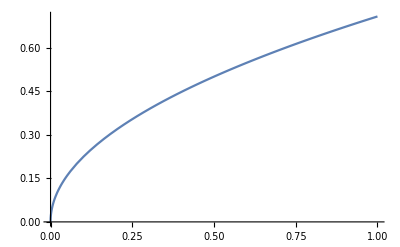

```mathematica
Contour:=Plot3D[f[x,y,β0],{x,0,1},{y,0,1},PlotStyle->Opacity[.5],MeshFunctions->{#3&},Mesh->7]
u:=Graphics3D[Arrow[{{.5, .5,.5},{1,1,1 }}]]
```

```mathematica
Show[Contour,u]
```

-Graphics3D-

```mathematica
Show[%43,ViewPoint->{1.3,-2.4,2.}]
```

-Graphics3D-